# Taller 1 - Introducción a Mathematica

## Mecánica Clásica 1

## Introducción:

#### Lenguaje de Wolfram

Wolfram es un lenguaje comúnmente utilizado para la programación científica. Es un lenguaje interpretado (al igual que Python), el cual tiene un paradigma de programación simbólica.

#### Interfaz

Wolfram Mathematica es a Wolfram, lo que Jupyter Notebook es a Python. Tiene la capacidad de realizar artículos, presentaciones y, obviamente, scripts (*.wls, *.nb) y módulos de rutinas (*.wl).

## Mathematica como Calculadora:

Primero que nada, ¿Cómo ejecutamos el código? Existen dos formas de hacerlo:
	- Ir al menu superior “Evaluation” -> “Evaluate Cells”.
	- Con la combinación de teclas Shift + Enter.

```mathematica
(* Podemos realizar operaciones aritméticas *)

(* Suma, resta, producto, división, exponenciación y división *)
6+4
3-9
5*7
7/3
6^6
√8
```

10

-6

35

7/3

46656

2 √2

Para poner las fracciones, exponentes y radicales chulos utilizamos las siguientes combinaciones de teclas:
	- Ctrl + /
	- Ctrl + 6
	- Ctrl + 2

```mathematica
(* Declaración de Variables *)
```

```mathematica
a = 1
H1 =1334
```

1

1334

```mathematica
(* quitar el valor de una variable *)
a=.
```

## Funciones (Rutinas)

A diferencia de en otros lenguajes, en Wolfram se utilizan los corchetes ‘[]’ en vez de ‘()’; además, toda rutina en Wolfram inicia con una letra mayuscula. Por ejemplo:

```mathematica
(* Resultado numérico de una operación *)
N[7/3] (* o *)
√8//N
```

2.33333

2.82843

```mathematica
(* Matriz identidad mostrada bonito *)
IdentityMatrix[6]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Derivadas *)
D[Sin[x],x] (* 1er orden *)
D[x^2*y+y^3,{x,2}] (* 2do orden (derivada parcial) *)
```

Cos[x]

2 y

```mathematica
(* Integrales *)
Integrate[Cos[x],x] (* Indefinida *)
Integrate[Cos[x],{x,0,π}] (* con límites *)
Integrate[1/(1+x^2),{x,-∞,∞}] (* Impropias *)
```

Sin[x]

0

π

```mathematica
(* Solución de Ecuaciónes y sistemas de ecuaciones (Algebraicas y diferenciales) *)
Solve[x^5+x^4+5 x^3+x^2+2x+1==0,x]//N
Solve[{2a+b-3c==7,5a-4b+c==19,a-b-4c==4},{a,b,c}] (* Sistema de ecuaciones *)
DSolve[x''[t]+ω^2*x[t]==0,x[t],t]
```

{{x→-0.415611},{x→-0.453826-2.07654 ⅈ},{x→-0.453826+2.07654 ⅈ},{x→0.161631-0.711644 ⅈ},{x→0.161631+0.711644 ⅈ}}

{{a→104/29,b→-8/29,c→-1/29}}

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

## Gráficas

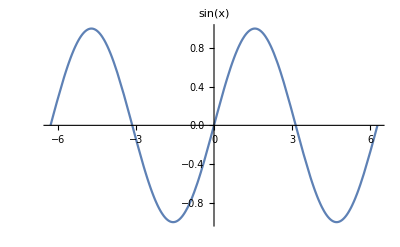

```mathematica
Plot[Sin[x],{x,-2*π,2*π},PlotLabel->Sin[x]]
```

```mathematica
PLeg[n_,x_]:=Simplify[1/(2^n*Factorial[n])*D[(x^2-1)^n,{x,n}]]
```

```mathematica
p=PLeg[#,x]&/@Range[0,5]
```

{1,x,1/2 (-1+3 x^2),1/2 x (-3+5 x^2),1/8 (3-30 x^2+35 x^4),1/8 x (15-70 x^2+63 x^4)}

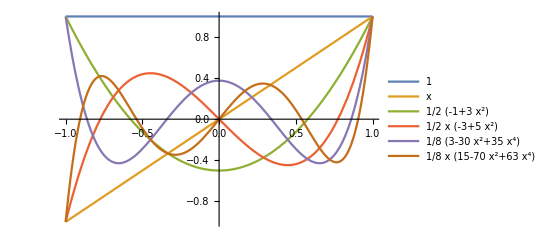

```mathematica
Plot[p,{x,-1,1},PlotLegends->"Expressions"]
```